```mathematica
Quit
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,FontSize->12,Magnification->1,"DisplayStyle"->True]
style=Directive[FontFamily->"LM Roman 12",FontSize->10];
cm=72/2.54;
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

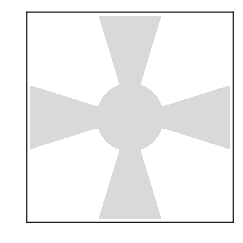

```mathematica
fs1 = 15;
fs2=10;
rps[Δr_, Δϕ_]:=RegionPlot[
{x^2 + y^2 ≤ Δr^2 ||
-Δϕ≤ ArcTan[y/x] ≤ Δϕ ||
Pi/2-Δϕ ≤ Abs@ArcTan[y/x] ≤ Pi/2+ Δϕ 

}


, {x, -3, 3}, {y, -3, 3}, 
BoundaryStyle->None,
PlotStyle->LightGray,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1,
FrameLabel->{MaTeX["\\text{Re}\\left(c\\right)", ContentPadding->False, FontSize->fs1],
MaTeX["\\text{Im}\\left(c\\right)", ContentPadding->False, FontSize->fs1]},
FrameTicks->None
]
fig=rps[1, 0.3]
```

```mathematica
Export[NotebookDirectory[]<>"\\rps.pdf", fig]
```

C:\Users\MatthewThornton\OneDrive for Business\Thesis\Writing\Images\qds\\rps.pdf